Transposition as a Supermap

Overviewpaclet:QuantumMob/QuantumPlaybook/tutorial/TranspositionAsASupermap#2075984682 | Positive, But Not Completely Positivepaclet:QuantumMob/QuantumPlaybook/tutorial/TranspositionAsASupermap#546624924
Operator-Sum Representationpaclet:QuantumMob/QuantumPlaybook/tutorial/TranspositionAsASupermap#792200605 |

Regarding transposition as a supermap, we find the Choi matrix and construct an explicit operator-sum representation of  the transposition supermap. The Choi matrix allows to quickly check that transposition is not completely positive.

Supermappaclet:QuantumMob/QuantumPlaybook/ref/SupermapQuantumMob Package Symbol | Rerepsents a supermap
PartialTransposepaclet:QuantumMob/QuantumPlaybook/ref/PartialTransposeQuantumMob Package Symbol | Returns the partial transposition of a linear operator
ChoiMatrixpaclet:QuantumMob/QuantumPlaybook/ref/ChoiMatrixQuantumMob Package Symbol | The Choi matrix of a supermap

Functions related to the transposition supermap.

Make sure to load Q3.

```mathematica
Needs["QuantumMob`Q3`"]
```

Overview

Recall the defining equation of the Choi matrix C of a supermap ℱ,

ℱ(ρ̂)=Σ_ij Σ_kl(F̂)_ij ρ̂(F̂)_kl^†C_(ij;kl) ,

where (F̂)_ij:=v_iv_j. An equivalent definition is

ℱ(v_kv_l)=Σ_ij v_i C_(ik;jl)v_j

with respect to a given orthonormal basis {v_k|k=1,2,…,d}.

The Choi matrix of the transposition supermap is given by

C_(ij;kl)=δ_jk δ_il.

Operator-Sum Representation

Let us consider a d-level system. The quantum levels are labeled by integers from 0 to d-1.

```mathematica
$d=3;
jj=Range[$d]-1
```

{0,1,2}

```mathematica
Let[Qudit,A,Dimension->$d]
```

We want to select a set of operators to span the supermaps that we are interested in; in this particular case, the standard basis of operators on the d-dimensional Hilbert space. We first construct all possible ordered pairs of level indices.

```mathematica
tpl=Tuples[jj,{2}]
```

{{0,0},{0,1},{0,2},{1,0},{1,1},{1,2},{2,0},{2,1},{2,2}}

Recalling that C_(ij;kl)=δ_jk δ_il the transposition supermap, we construct the list of reversed pairs from the previously constructed list of ordered pairs.

```mathematica
rvs=Reverse/@tpl
```

{{0,0},{1,0},{2,0},{0,1},{1,1},{2,1},{0,2},{1,2},{2,2}}

We then construct the set of operators from the above ordered pairs.

```mathematica
ops=Map[A,Rule@@@rvs]
```

{(00),(01),(02),(10),(11),(12),(20),(21),(22)}

### Using Graph

Here is one way to get the Choi matrix for transposition: using graph and its adjacency matrix.

Construct the edges.

```mathematica
edges=Thread[tpl->rvs]
```

{{0,0}→{0,0},{0,1}→{1,0},{0,2}→{2,0},{1,0}→{0,1},{1,1}→{1,1},{1,2}→{2,1},{2,0}→{0,2},{2,1}→{1,2},{2,2}→{2,2}}

In many cases, you do not have to specify the vertices explicitly. However, in this case, doing it is necessary to keep the order of vortices as we want.

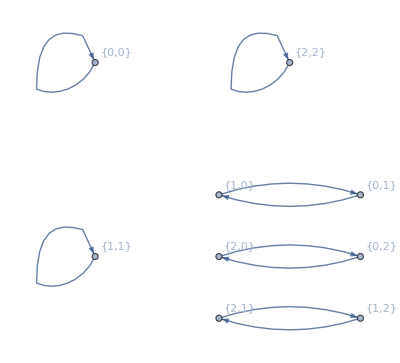

```mathematica
grf=Graph[tpl,edges,VertexLabels->"Name"]
```

```mathematica
mat=AdjacencyMatrix[grf];
mat//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

With the Choi matrix given, construct the supermap.

```mathematica
spr=Supermap[ops,mat];
```

To verify the supermap, think of a few examples of input operators.

```mathematica
in=A[0->2]
```

(20)

```mathematica
out=spr[in]
```

(02)

```mathematica
in=A[0->2]+I*A[1->2]
```

(20)+ⅈ (21)

```mathematica
out=spr[in]
```

(02)+ⅈ (12)

Note that this is different from the Hermitian conjugate.

```mathematica
Dagger[in]
```

(02)-ⅈ (12)

### Using Permutation

Here is another method to get the Choi matrix: using permutation matrix.

```mathematica
prm=FindPermutation[tpl,rvs]
```

Cycles[{{2,4},{3,7},{6,8}}]

```mathematica
new=PermutationMatrix[prm,9];
new//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
mat-new//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

Positive, But Not Completely Positive

Let us further analyse the Choi matrix using its spectral decomposition.

```mathematica
{val,vec}=Eigensystem[mat];
```

First, note that the Choi matrix has some negative eigenvalues and hence is not positive (semi-definite). This implies that the corresponding supermap ℱ is not completely positive even though it is obviously positive.

```mathematica
val
```

{-1,-1,-1,1,1,1,1,1,1}

Now, let us optimize the operator-sum representation. Before doing that, check the eigenvectors are orthonormal to each other.

```mathematica
Topple[vec].vec//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

It turns out that they are orthogonal to each other, but are not normalized. Just normalization suffices.

```mathematica
trs=Normalize/@vec;
Topple[trs].trs//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
obs=trs.ops
```

{(21)/(√2)-(12)/(√2),(20)/(√2)-(02)/(√2),(10)/(√2)-(01)/(√2),(22),(21)/(√2)+(12)/(√2),(20)/(√2)+(02)/(√2),(11),(10)/(√2)+(01)/(√2),(00)}

Double check that they are orthogonal to each other with respect to the Hilbert-Schmidt inner product.

```mathematica
chk=Outer[HilbertSchmidtProduct,Matrix/@obs,Matrix/@obs,1];
chk//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

Finally, let us construct the supermap in terms of this new set of operators and the eigenvalues.

```mathematica
new=Supermap[obs,val];
```

Check that this new specification of the supermap produces the same result.

```mathematica
in
```

(20)+ⅈ (21)

```mathematica
new[in]
```

(02)+ⅈ (12)

The fact that the transposition supermap is not completely positive can be seen applying the partial transposition, i.e., ℱ⊗ℐ on the composite system of the “system” and any “environment”. For example, let us consider the maximally entangled state in 𝒱⊗𝒱.

```mathematica
ket=Total@Multiply[Basis[A],Basis[A[E]]]/Sqrt[Dimension@A]
```

(0_A0_A_ⅇ+1_A1_A_ⅇ+2_A2_A_ⅇ)/(√3)

Take the dyadic product of it with itself to construct the (pure-state) density operator.

```mathematica
in=Dyad[ket,ket,{A,A[E]}]
```

1/3 0_A0_A_ⅇ0_A0_A_ⅇ+1/3 0_A0_A_ⅇ1_A1_A_ⅇ+1/3 0_A0_A_ⅇ2_A2_A_ⅇ+1/3 1_A1_A_ⅇ0_A0_A_ⅇ+1/3 1_A1_A_ⅇ1_A1_A_ⅇ+1/3 1_A1_A_ⅇ2_A2_A_ⅇ+1/3 2_A2_A_ⅇ0_A0_A_ⅇ+1/3 2_A2_A_ⅇ1_A1_A_ⅇ+1/3 2_A2_A_ⅇ2_A2_A_ⅇ

Obviously, as a pure state, it only has non-negative eigenvalues.

```mathematica
ProperValues[in]
```

{1,0,0,0,0,0,0,0,0}

What about the partial transposition.

```mathematica
out=PartialTranspose[in,A]
```

1/3 (00)(00)_ⅇ+1/3 (10)(01)_ⅇ+1/3 (20)(02)_ⅇ+1/3 (01)(10)_ⅇ+1/3 (11)(11)_ⅇ+1/3 (21)(12)_ⅇ+1/3 (02)(20)_ⅇ+1/3 (12)(21)_ⅇ+1/3 (22)(22)_ⅇ

```mathematica
ProperValues[out]
```

{-1/3,-1/3,-1/3,1/3,1/3,1/3,1/3,1/3,1/3}

In fact, according to the Choi isomorphism, out is the Choi operator (up to a normalization factor).

```mathematica
iso=3*Matrix[out];
iso//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
iso-mat//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

| Related Guides
▪Quantum Computation and Information

| Related Tech Notes
▪A Quantum Playbook
▪Choi Isomorphism
▪Quantum Noise and Decoherence

| Related Links
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer, 2022).